{{Y[X]→1/(12 ⅇ)A (3 Cos[√3]-3 ⅇ^(1+X) Cos[√3 X]+√3 Sin[√3]+√3 ⅇ^(1+X) Sin[√3 X])}}

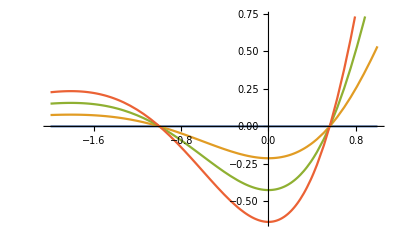

```mathematica
eqn:=Y'''[X]-2*Y''[X]+4*Y'[X];
s=DSolve[{eqn==0,Y[-1]==0,Y'[0]==0,Y''[0]==A},Y[X],X]
Plot[Evaluate[Y[X]/. s/. A->Range[0,3]],{X,1,-2}]
```

{{Y[X]→-1/2 ⅇ^-X (-2-A-2 ⅇ^X Cos[X]+A ⅇ^X Cos[X]-A ⅇ^X Sin[X])}}

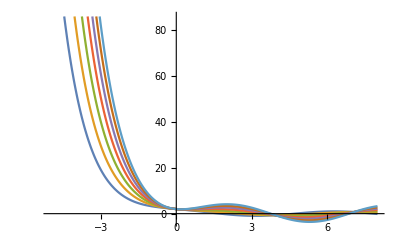

```mathematica
eqn:=Y'''[X]+Y''[X]+Y'[X]+Y[X];
s=DSolve[{eqn==0,Y[0]==2,Y'[0]==-1,Y''[0]==A},Y[X],X]
Plot[Evaluate[Y[X]/. s/. A->Range[0,6]],{X,-5,8}]
```

{{Y[X]→-2/15 A ⅇ^-X (-3+3 ⅇ^(5 X/4) Cos[(√15 X)/4]-√15 ⅇ^(5 X/4) Sin[(√15 X)/4])}}

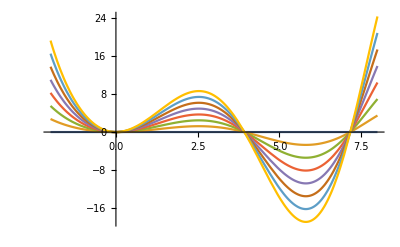

```mathematica
e1:= 2*Y'''[X]+Y''[X]+Y'[X]+2*Y[X];
S=DSolve[{e1==0,Y[0]==0,Y'[0]==0,Y''[0]==A},Y[X],X]
Plot[Evaluate[Y[X]/.S/. A-> Range[0,7]],{X,-2,8}]
```